## 1d optimal control, unstable case (Problem 9.8)

```mathematica
Clear["Global`*"];
```

nominal optimal control problem (with the variable a known exactly)

```mathematica
eqs={x'[t]-a x[t]==u[t],u[t]==-k x[t]};init={x[0]==1};

{xs,us}=DSolveValue[{eqs,init},{x[t],u[t]},t]
```

{ⅇ^((a-k) t),-ⅇ^((a-k) t) k}

```mathematica
J=Integrate[(xs^2+us^2),{t,0,∞}, Assumptions->k>a>0] //Factor
```

-(1+k^2)/(2 (a-k))

```mathematica
{k0=k/.Solve[D[J, k]==0,k][[2,1]],k00=k0/.a->1,k00//N}
```

{a+√(1+a^2),1+√2,2.41421}

```mathematica
{J0=J/.k->k0,J00=J0/.a->1,J00//N}//FullSimplify
```

{a+√(1+a^2),1+√2,2.41421}

lognormal distribution for a

```mathematica
μ=-1/2 Log[1+ϵ^2]; σ=√(-2μ); 
adist=LogNormalDistribution[μ,σ]; pa=Simplify[PDF[adist,a],Assumptions->{a>0,ϵ>0}];{Mean[adist],Variance[adist]}
```

{1,ϵ^2}

```mathematica
amax[α_,ϵ0_]:=InverseSurvivalFunction[adist,α]/.ϵ->ϵ0
amax[0.01,0.5]
```

2.68411

Optimize feedback gain k over the restricted system range of (0, amax)

```mathematica
{pa,PDF[LogNormalDistribution[μ,σ],a],J}
```

{(ⅇ^(-((2 Log[a]+Log[1+ϵ^2])^2)/(8 Log[1+ϵ^2])))/(a √(2 π) √Log[1+ϵ^2]),Piecewise[{{(ⅇ^(-((Log[a]+1/2 Log[1+ϵ^2])^2)/(2 Log[1+ϵ^2])))/(a √(2 π) √Log[1+ϵ^2]), a>0}, {0, True}}],-(1+k^2)/(2 (a-k))}

```mathematica
paJ[k0_,a0_,ϵ0_]:=Simplify[pa J/.{k->k0,a->a0,ϵ->ϵ0},Assumptions->{k>a>0,ϵ>0}];paJ[k,a,ϵ]
```

-(ⅇ^(-((2 Log[a]+Log[1+ϵ^2])^2)/(8 Log[1+ϵ^2])) (1+k^2))/(2 a (a-k) √(2 π) √Log[1+ϵ^2])

```mathematica
Jgood[k_,α_,ϵ_]:=NIntegrate[paJ[k,a,ϵ],{a,0,amax[α,ϵ]}]; Jgood[2,0.01,0.2]
```

2.56321

```mathematica
JgoodMin[α_,ϵ_]:=Module[{amaxVal=amax[α,ϵ],JminVal,ks},JminVal=FindMinimum[{Jgood[k,α,ϵ],k>amax[α,ϵ]},{k,amax[α,ϵ]+0.2}]/.{α->0.01,ϵ->0.5}//Quiet;{ks=k/.JminVal[[2]]};{JminVal[[1]],ks}]
```

```mathematica
JgoodMin[0.01,0.5]
```

{2.65697,3.07385}

```mathematica
{Jmin,kstar}=Table[JgoodMin[0.01,ϵ],{ϵ,0.1,1,0.1}]ᵀ;
```

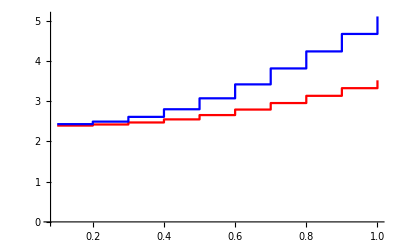

```mathematica
p1=ListPlot[{Jmin,kstar},Joined->True,DataRange->{0.1,1},PlotStyle->{Red,Blue}]
(* plot exact minimized Jgood and kstar   optimized over (0,amax) *)
```

Perturbative calculation  (dimensional version; simple enough not to scale)

```mathematica
βstar=-1/2 1/k00(D[J, a,a,k]/D[J, k,k])/.{k->k00,a->1}//Simplify (* perturbation formula *)
```

1

```mathematica
kpert=k00(1+βstar ϵ^2);    (* perturbative result *)
```

```mathematica
ϵmax=ϵ/.FindRoot[amax[0.01,ϵ]==kpert,{ϵ,0.7}]  (* max allowed ϵ for pert soln *)
```

0.736409

```mathematica
{amax[0.01,ϵmax],JgoodMin[0.01,ϵmax]}
```

{3.72344,{3.01997,3.96927}}

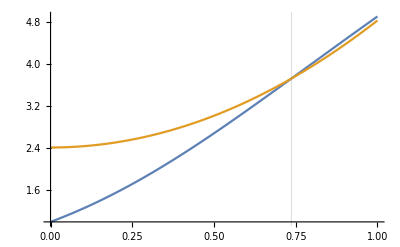

```mathematica
p0=Plot[{amax[0.01,ϵ],kpert},{ϵ,0,1},GridLines->{{ϵmax},{}}]
```

```mathematica
Jpert[ϵ0_]:=Jgood[kpert/.ϵ->ϵ0,0.01,ϵ0]
Jpert[0.2]
```

2.42311

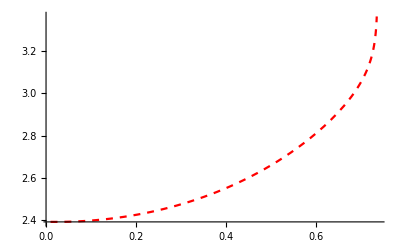

```mathematica
p3=Plot[Jpert[ϵ],{ϵ,0.01,ϵmax},PlotStyle->{Red,Dashed}]
```

```mathematica
JpertExtra=Table[Jpert[ϵ],{ϵ,ϵmax-10^-3,ϵmax,10^-5}]//Quiet;
```

```mathematica
p2=Plot[kpert,{ϵ,0,ϵmax},PlotStyle->{{Blue,Dashed}},GridLines->{{ϵmax},{}}];
```

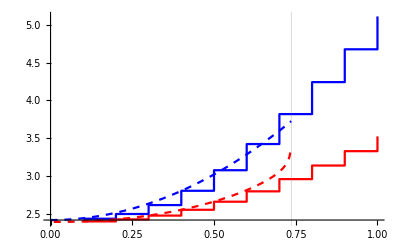

```mathematica
Show[{p2,p1,p3},PlotRange->All]
```

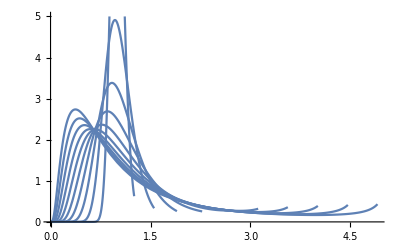

```mathematica
Show[Table[Plot[paJ[kstar[[i]],a,0.1i],{a,0,amax[0.01,0.1i]},PlotRange->{0,5}],{i,10,1,-1}]]//Quiet
```

Explore adaptive approach

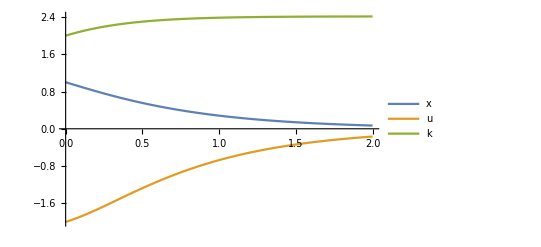

```mathematica
tmax=2;
eqs1={x'[t]-a x[t]==u[t],u[t]==-k[t] x[t],k'[t]==γ( x[t])^2,x[0]==1,k[0]==2};
{xs1,us1,ks1}=NDSolveValue[eqs1/.{a->1,γ->1},{x[t],u[t],k[t]},{t,0,tmax}];
Plot[{xs1,us1,ks1},{t,0,tmax},PlotRange->All,PlotLegends->{x,u,k}]
```

Export data

```mathematica
dt=0.01;
dat1=Table[amax[dt,ϵ],{ϵ,dt,1,dt}];
JpertPoints=Cases[p3,Line[data_] :> data,-4,1][[1]];
(* 
SetDirectory[NotebookDirectory[]];Export["firstOrderUnstable_dat1.dat", dat1];Export["firstOrderUnstable_dat2.dat", JpertPoints];
Export["firstOrderUnstable_dat2a.dat", JpertExtra];
Export["firstOrderUnstable_dat3.dat",{Jmin,kstar}ᵀ];
*)
```